```mathematica
Clear["Global`*"]
Needs["ErrorBarPlots`"]
fermi = 1;
If[fermi == 1,SetDirectory[StringJoin[NotebookDirectory[],"/Fermions"]],SetDirectory[StringJoin[NotebookDirectory[],"/Bosons"]]];
λ=1.0;
τ=0.001;
σ=√(λ τ);
μ=0;
```

```mathematica
points=Import["numTrace.txt","List"];
```

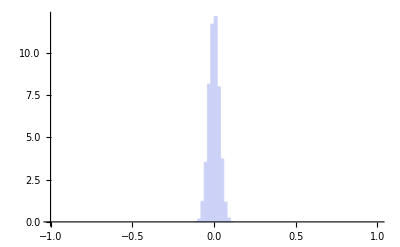

```mathematica
pointsHist=Histogram[points,100,"ProbabilityDensity"]
```

```mathematica
pointsPlot=ListPlot[points];
dist = 1/(√(2π σ^2))E^((-(x-μ)^2)/(2 σ^2));
```

```mathematica
Integrate[dist,{x,-∞,∞}]
```

1.

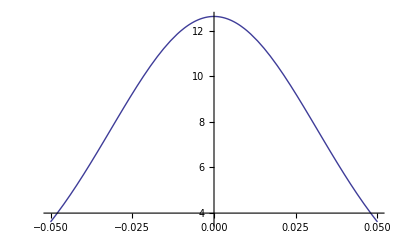

```mathematica
distPlot=Plot[dist,{x,-0.05,0.05}]
```

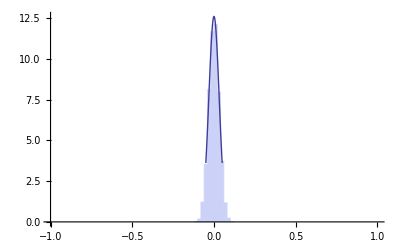

```mathematica
Show[pointsHist,distPlot]
```